# Fundamentally fastest optical processes at the surface of a topological insulator

## TI Bi2Se3 Hamiltonian

```mathematica
Clear["Global`*"]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
H0=({{A1 (qx^2+qy^2)+A3 ( (qx+ⅈ qy)^3+(qx-ⅈ qy)^3), A2 (qy +ⅈ qx)}, {A2 (qy -ⅈ qx), A1 (qx^2+qy^2)-A3 ( (qx+ⅈ qy)^3+(qx-ⅈ qy)^3)}});
```

```mathematica
val=Chop[Eigenvalues[H0]]
```

{A1 qx^2+A1 qy^2-√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4),A1 qx^2+A1 qy^2+√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)}

```mathematica
E1v[qx_,qy_]=val[[1]]
```

A1 qx^2+A1 qy^2-√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)

```mathematica
E2c[qx_,qy_]=val[[2]]
```

A1 qx^2+A1 qy^2+√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)

```mathematica
E2c[-1,-1]//FullSimplify
```

2 A1+√(2 A2^2+16 A3^2)

```mathematica
eivec=Chop[Eigenvectors[H0]]
```

{{(ⅈ (2 A3 qx^3-6 A3 qx qy^2-√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx+ⅈ qy)),1},{(ⅈ (2 A3 qx^3-6 A3 qx qy^2+√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx+ⅈ qy)),1}}

```mathematica
evecV[qx_,qy_] = eivec[[1]];
```

```mathematica
evecVd={{(-ⅈ (2 A3 qx^3-6 A3 qx qy^2-√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx-ⅈ qy)),1}};
```

```mathematica
M=(evecVd . evecV[qx,qy])⟦1⟧//Simplify
```

2-(4 A3 qx (qx^2-3 qy^2) (-2 A3 qx^3+6 A3 qx qy^2+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(A2^2 (qx^2+qy^2))

```mathematica
MevecV[qx_,qy_] = 1/(√M)eivec[[1]]
```

{(ⅈ (2 A3 qx^3-6 A3 qx qy^2-√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx+ⅈ qy) √(2-(4 A3 qx (qx^2-3 qy^2) (-2 A3 qx^3+6 A3 qx qy^2+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(A2^2 (qx^2+qy^2)))),1/(√(2-(4 A3 qx (qx^2-3 qy^2) (-2 A3 qx^3+6 A3 qx qy^2+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(A2^2 (qx^2+qy^2))))}

```mathematica
MevecVd[qx_,qy_]=1/(√M){{(-ⅈ (2 A3 qx^3-6 A3 qx qy^2-√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx-ⅈ qy)),1}};
```

```mathematica
(MevecVd[qx,qy].MevecV[qx,qy])⟦1⟧//Simplify
```

1

```mathematica
evecC[qx_,qy_]= eivec[[2]];
```

```mathematica
evecCd[qx_,qy_]={{(-ⅈ (2 A3 qx^3-6 A3 qx qy^2+√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx-ⅈ qy)),1}};
```

```mathematica
Μ=(evecCd[qx,qy]. evecC[qx,qy])⟦1⟧//Simplify;
```

```mathematica
ΜevecC[qx_,qy_] = 1/(√Μ)eivec[[2]]
```

{(ⅈ (2 A3 qx^3-6 A3 qx qy^2+√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx+ⅈ qy) √(2+(4 A3 qx (qx^2-3 qy^2) (2 A3 (qx^3-3 qx qy^2)+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(A2^2 (qx^2+qy^2)))),1/(√(2+(4 A3 qx (qx^2-3 qy^2) (2 A3 (qx^3-3 qx qy^2)+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(A2^2 (qx^2+qy^2))))}

```mathematica
ΜevecCd[qx_,qy_] =1/(√Μ){{(-ⅈ (2 A3 qx^3-6 A3 qx qy^2+√(A2^2 qx^2+4 A3^2 qx^6+A2^2 qy^2-24 A3^2 qx^4 qy^2+36 A3^2 qx^2 qy^4)))/(A2 (qx-ⅈ qy)),1}};
```

```mathematica
( ΜevecCd[qx,qy]. ΜevecC[qx,qy])[[1]]//Simplify;
```

```mathematica
Αx=-ⅈ  D[MevecV[qx,qy] , qx];
```

```mathematica
Ax[qx_,qy_]=(ΜevecCd[qx,qy]. Αx)[[1]]//FullSimplify
```

(-2 ⅈ A3 (2 qx^4+3 qx^2 qy^2-3 qy^4)-qy √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 (qx^2+qy^2) √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)) √(1+1/(-1-(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))) √(1+1/(-1+(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))))

```mathematica
Axcc[qx_ ,qy_]=(2 ⅈ A3 (2 qx^4+3 qx^2 qy^2-3 qy^4)-qy √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 (qx^2+qy^2) √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)) √(1+1/(-1-(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))) √(1+1/(-1+(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))));
```

```mathematica
absAx[qx_,qy_]=√(Ax[qx,qy]*Axcc[qx,qy])//FullSimplify
```

1/2 √((A2^4 qy^2+4 A2^2 A3^2 (4 qx^6+9 qx^4 qy^2-18 qx^2 qy^4+9 qy^6))/((4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))^2))

```mathematica
argx[qx_,qy_]=  Arg[(-2 ⅈ A3 (2 qx^4+3 qx^2 qy^2-3 qy^4)-qy √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 (qx^2+qy^2) √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))];
```

```mathematica
Αy=-ⅈ  D[MevecV[qx,qy] , qy];
```

```mathematica
Ay[qx_,qy_]=(ΜevecCd[qx,qy]. Αy)[[1]]//FullSimplify
```

(qx (2 ⅈ A3 (7 qx^2 qy+3 qy^3)+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(2 (qx^2+qy^2) √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)) √(1+1/(-1-(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))) √(1+1/(-1+(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))))

```mathematica
Aycc[qx_,qy_]=(qx (-2 ⅈ A3 (7 qx^2 qy+3 qy^3)+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(2 (qx^2+qy^2) √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)) √(1+1/(-1-(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))) √(1+1/(-1+(√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))/(2 A3 qx (qx^2-3 qy^2)))));
```

```mathematica
absAy[qx_,qy_]=√(Ay[qx,qy]* Aycc[qx,qy])//FullSimplify
```

1/2 √((A2^2 qx^2 (A2^2+4 A3^2 (qx^4+42 qx^2 qy^2+9 qy^4)))/((4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))^2))

```mathematica
argy[qx_,qy_]=Arg[(qx (2 ⅈ A3 (7 qx^2 qy+3 qy^3)+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/(2 (qx^2+qy^2) √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))]
```

Arg[(qx (2 ⅈ A3 (7 qx^2 qy+3 qy^3)+√(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2))))/((qx^2+qy^2) √(4 A3^2 qx^2 (qx^2-3 qy^2)^2+A2^2 (qx^2+qy^2)))]

```mathematica
Ω=Curl[{Ax [qx,qy],Ay[qx,qy]},{qx , qy}]//FullSimplify;
```

## Linearly polarized pulse

```mathematica
A1=23.725;A2=3.297;A3=25.045;
```

```mathematica
(* [ℏ]=eVfs , [t]=fs , [e]=1 , [k]=Å^-1 , [F]=V/Å *)
```

```mathematica
ℏ=0.658209; e=1;c=1;G=1;ϵ0=1;T=1;F0=0.1;
```

```mathematica
Fx[t_]=F0(1-2(t/T)^2)Exp[-(t/T)^2]Cos[θ];
```

```mathematica
Fy[t_]=F0(1-2(t/T)^2)Exp[-(t/T)^2]Sin[θ];
```

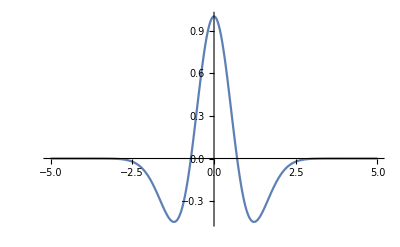

```mathematica
Plot[(1-2(t/1)^2)Exp[-(t/1)^2], {t,-5,5} , PlotRange->Full]
```

```mathematica
f1x[t_]:=(1/ ℏ)∫_(-∞)^t Fx[t']ⅆ t'
```

```mathematica
f1x[t]
```

0.151927 ⅇ^(-t^2) t Cos[θ]

```mathematica
f1y[t_]:=(1/ ℏ)∫_(-∞)^t Fy[t']ⅆ t'
```

```mathematica
f1y[t]
```

0.151927 ⅇ^(-t^2) t Sin[θ]

```mathematica
Kx[qx_ ,t_]:=qx+ 0.1519274273065242 ⅇ^(-t^2) t Cos[θ];
```

```mathematica
Ky[qy_ ,t_]:=qy +0.1519274273065242 ⅇ^(-t^2) t Sin[θ]
```

```mathematica
KK[qx_,qy_,t_]:=√(Kx[qx,t]^2+Ky[qy,t]^2)
```

```mathematica
KK[qx,qy,t]
```

√((qx+0.151927 ⅇ^(-t^2) t Cos[θ])^2+(qy+0.151927 ⅇ^(-t^2) t Sin[θ])^2)

```mathematica
Δ[t_]:=((1/ ℏ)(E2c[Kx[qx,t],Ky[qy,t]]-E1v[Kx[qx,t],Ky[qy,t]])-(1/ ℏ)(E2c[qx,qy]-E1v[qx,qy]))//FullSimplify
```

```mathematica
ϕ[t_]:=NIntegrate[Δ[z] ,{z, -3.5, t}]
```

```mathematica
{Fx[t] ,Fy[t]}.{Ax[Kx[qx ,t],Ky[qy  ,t]] , Ay[Kx[qx ,t],Ky[qy ,t]]};
```

```mathematica
f[t_,x_,y_]:=If[KK[qx,qy,t]≤10^-5,0, -ⅈ(1/ ℏ)({Fx[t] ,Fy[t]}.{Ax[Kx[qx,t],Ky[qy,t]] , Ay[Kx[qx,t],Ky[qy,t]]})Exp[ⅈ ϕ[t]] y ]
```

```mathematica
g[t_,x_,y_]:=If[KK[qx,qy,t]≤10^-5,0,-ⅈ(1/ ℏ)({Fx[t] ,Fy[t]}.Conjugate[{Ax[Kx[qx,t],Ky[qy,t]] , Ay[Kx[qx,t],Ky[qy,t]]}Exp[ⅈ ϕ[t]]]) x]
```

```mathematica
t1=3.5;t0=-3.5; x0=0 ; y0=1 ;Q={0,Pi/4,Pi/3,Pi/2};
```

```mathematica
n=50;(* number of subintervals *)
```

```mathematica
h=(t1-t0)/n ;(* step size *)
```

```mathematica
For[j=1,j≤4,j+=1,{
θ=Q[[j]];
SS={};
For[qx=-0.8,qx≤0.8,qx+=0.08,{
For[qy=-0.8,qy≤0.8,qy+=0.08,{
Clear[x,y,t];
y=y0;x=x0;t=t0;
For[i=1,i≤n,i+=1,{
K1=f[t,x,y];                                                           (* right-hand slopes *)
L1=g[t,x,y];                                                           (* left-hand slopes *)
K2=f[t+h/2,x+h* K1/2,y+h*L1/2];
L2=g[t+h/2,x+h* K1/2,y+h*L1/2];  (*1st midpt slopes*)
K3=f[t+h/2,x+h* K2/2,y+h*L2/2];
L3=g[t+h/2,x+h* K2/2,y+h*L2/2];  (*2nd midpt slopes*)
K4=f[t+h,x+h* K3,y+h*L3];
L4=g[t+h,x+h* K3,y+h*L3];
k=(K1+2*K2+2*K3+K4)/6;                            (*average x-slope*)
l=(L1+2*L2+2*L3+L4)/6;                            (*average y-slope*)
x=x+h*k;                                                                 (*update x*)
y=y+h*l;                                                                 (*update y*)
t=t+h;                                                                       (*update t*)
xd=Conjugate[x];
If[i==n,
X=AppendTo[SS,{qx,qy,Re[x*xd]}]] (*display each mth value*)}]
}]}];
Print[X];
ListDensityPlot[X, ColorFunction->"Rainbow",PlotRange->{0,1},PlotLegends->Automatic, Mesh->Full],
Length[X];
ListPlot3D[X,PlotRange->Full]
}]
```

$Aborted